```mathematica
TableForm[Table[QuadrilateralPattern[k],{k,Range[5]}],TableDepth->2]
```

{1,3} | {2} | {4} | {5}
{1} | {2,4} | {3} | {5}
{1} | {2} | {3,5} | {4}
{1,4} | {2} | {3} | {5}
{1} | {2,5} | {3} | {4}

```mathematica
QuadrilateralPattern[5]
```

{{1},{2,5},{3},{4}}

```mathematica
Clear[ShowForNodesTwo];ShowForNodesTwo[nodes_]:=Flatten[Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]]
},
{Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2]]]], SymbolLevel[#]==4&],{part1,part2}}
]
,

{part1,QuadrilateralsWithPattern[nodes,1]},
{part2,QuadrilateralsWithPattern[nodes,5]}
],1]
```

```mathematica
ShowForNodesTwo[6]
```

{{{v16x24x3x5,v13x26x4x5,v13x24x5x6},{{{1,3},{2,6},{4},{5}},{{1,6},{2,4},{3},{5}}}},{{v1x24x36x5,v13x26x4x5,v13x24x5x6},{{{1,3},{2,6},{4},{5}},{{1},{2,4},{3,6},{5}}}},{{v1x24x3x56,v13x2x4x56,v13x26x4x5,v13x24x5x6},{{{1,3},{2,6},{4},{5}},{{1},{2,4},{3},{5,6}}}},{{v1x246x3x5,v13x2x46x5,v13x26x4x5,v13x24x5x6},{{{1,3},{2,6},{4},{5}},{{1},{2,4,6},{3},{5}}}},{{v16x24x3x5,v13x2x46x5,v13x24x5x6},{{{1,3},{2},{4,6},{5}},{{1,6},{2,4},{3},{5}}}},{{v1x24x36x5,v13x2x46x5,v13x24x5x6},{{{1,3},{2},{4,6},{5}},{{1},{2,4},{3,6},{5}}}},{{v1x24x3x56,v13x2x4x56,v13x2x46x5,v13x24x5x6},{{{1,3},{2},{4,6},{5}},{{1},{2,4},{3},{5,6}}}},{{v1x246x3x5,v13x2x46x5,v13x26x4x5,v13x24x5x6},{{{1,3},{2},{4,6},{5}},{{1},{2,4,6},{3},{5}}}},{{v1x24x3x56,v16x24x3x5,v13x2x4x56,v13x24x5x6},{{{1,3},{2},{4},{5,6}},{{1,6},{2,4},{3},{5}}}},{{v1x24x3x56,v1x24x36x5,v13x2x4x56,v13x24x5x6},{{{1,3},{2},{4},{5,6}},{{1},{2,4},{3,6},{5}}}},{{v1x24x3x56,v13x2x4x56,v13x24x5x6},{{{1,3},{2},{4},{5,6}},{{1},{2,4},{3},{5,6}}}},{{v1x246x3x5,v1x24x3x56,v13x2x4x56,v13x2x46x5,v13x26x4x5,v13x24x5x6},{{{1,3},{2},{4},{5,6}},{{1},{2,4,6},{3},{5}}}},{{v1x24x36x5,v16x24x3x5,v136x2x4x5,v13x24x5x6},{{{1,3,6},{2},{4},{5}},{{1,6},{2,4},{3},{5}}}},{{v1x24x36x5,v16x24x3x5,v136x2x4x5,v13x24x5x6},{{{1,3,6},{2},{4},{5}},{{1},{2,4},{3,6},{5}}}},{{v1x24x3x56,v1x24x36x5,v16x24x3x5,v136x2x4x5,v13x2x4x56,v13x24x5x6},{{{1,3,6},{2},{4},{5}},{{1},{2,4},{3},{5,6}}}},{{v1x246x3x5,v1x24x36x5,v16x24x3x5,v136x2x4x5,v13x2x46x5,v13x26x4x5,v13x24x5x6},{{{1,3,6},{2},{4},{5}},{{1},{2,4,6},{3},{5}}}}}

```mathematica
Map[Length[#[[1]]]&,ShowForNodesTwo[6]]
```

{3,3,4,4,4,4,3,6,3,3,4,4,4,4,6,7}

```mathematica
Map[{Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]],Length[Select[#[[1]],HasQuadrilateralPattern[SymbolToSets[#]]&]]}&,ShowForNodesTwo[7]]//Tally//Sort
```

{{{0,2},4},{{1,2},36},{{1,3},16},{{2,2},8},{{2,3},40},{{2,4},56},{{3,2},1},{{3,3},8},{{3,5},32},{{3,6},2},{{3,7},8},{{3,8},8},{{4,5},4},{{4,7},8},{{4,8},8},{{4,9},8},{{4,10},2},{{5,13},2},{{5,15},4},{{5,18},1}}

```mathematica
Map[{Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]],Length[Select[#[[1]],HasQuadrilateralPattern[SymbolToSets[#]]&]]}&,ShowForNodesTwo[8]]//Tally//Sort
```

{{{0,2},132},{{0,3},72},{{1,2},316},{{1,3},288},{{1,5},24},{{2,2},120},{{2,3},432},{{2,4},372},{{2,5},96},{{2,6},48},{{3,3},48},{{3,4},144},{{3,5},48},{{3,6},24},{{4,2},24},{{4,3},60},{{4,4},96},{{4,5},120},{{4,6},504},{{4,8},84},{{5,5},24},{{5,6},12},{{5,7},84},{{6,7},24},{{6,9},48},{{6,10},48},{{6,11},72},{{7,2},1},{{7,3},12},{{7,5},48},{{7,6},3},{{7,8},48},{{7,9},92},{{7,10},48},{{7,11},36},{{7,12},36},{{8,10},24},{{8,11},24},{{8,13},48},{{9,15},24},{{9,17},12},{{9,18},3},{{9,22},12},{{10,5},6},{{10,7},24},{{10,11},24},{{10,14},24},{{10,15},24},{{11,10},6},{{11,15},12},{{11,19},24},{{11,21},24},{{12,22},6},{{14,13},6},{{14,17},12},{{14,22},12},{{14,24},24},{{14,27},12},{{15,30},6},{{19,35},2},{{19,39},6},{{19,45},6},{{19,54},1}}

```mathematica
Map[{Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]],Length[Select[#[[1]],HasQuadrilateralPattern[SymbolToSets[#]]&]]}&,ShowForNodesTwo[9]]//Tally//Sort
```

{{{0,2},3652},{{0,3},2592},{{0,5},432},{{1,2},3732},{{1,3},3584},{{1,5},576},{{1,9},32},{{2,2},1328},{{2,3},4864},{{2,4},4752},{{2,5},1920},{{2,6},1056},{{2,7},96},{{2,9},96},{{2,10},96},{{3,3},1056},{{3,4},1872},{{3,5},192},{{3,6},528},{{4,2},480},{{4,3},768},{{4,4},480},{{4,5},2304},{{4,6},3744},{{4,7},576},{{4,8},1800},{{4,9},192},{{4,10},384},{{4,12},96},{{5,3},192},{{5,4},240},{{5,5},288},{{5,6},864},{{5,7},576},{{5,10},96},{{6,5},240},{{6,6},624},{{6,7},288},{{6,8},2232},{{6,9},192},{{6,12},96},{{7,7},96},{{7,9},48},{{8,2},48},{{8,3},208},{{8,4},336},{{8,5},96},{{8,6},624},{{8,8},48},{{8,9},416},{{8,10},1808},{{8,12},1056},{{8,16},240},{{9,5},48},{{9,7},192},{{9,8},72},{{9,9},48},{{9,10},192},{{9,11},280},{{9,12},288},{{9,14},192},{{10,9},48},{{10,11},384},{{10,13},48},{{10,14},288},{{10,15},144},{{11,6},48},{{11,7},48},{{11,9},144},{{11,13},480},{{11,14},192},{{11,16},384},{{12,7},48},{{12,9},96},{{12,13},144},{{12,14},144},{{12,15},192},{{12,16},288},{{12,17},288},{{13,8},48},{{13,10},192},{{13,14},288},{{13,16},192},{{13,18},192},{{14,11},96},{{14,12},48},{{14,14},48},{{14,15},96},{{14,19},192},{{14,20},96},{{15,2},1},{{15,3},16},{{15,5},96},{{15,6},4},{{15,8},48},{{15,9},112},{{15,11},48},{{15,12},48},{{15,17},376},{{15,19},64},{{15,20},16},{{16,13},96},{{16,15},96},{{16,16},48},{{16,19},48},{{16,21},48},{{17,18},6},{{17,21},96},{{17,22},48},{{17,25},144},{{17,27},24},{{17,30},24},{{18,10},96},{{18,17},48},{{18,19},48},{{18,21},48},{{18,23},192},{{18,26},96},{{18,27},48},{{18,31},144},{{19,25},96},{{20,24},96},{{20,28},192},{{20,30},192},{{21,27},96},{{21,29},96},{{21,31},48},{{22,5},8},{{22,7},48},{{22,11},96},{{22,19},64},{{22,22},48},{{22,25},48},{{22,26},64},{{22,27},64},{{22,35},96},{{23,15},24},{{23,19},96},{{23,22},48},{{23,25},48},{{23,26},96},{{23,27},48},{{23,33},96},{{23,36},48},{{25,10},12},{{25,35},48},{{27,43},16},{{27,54},4},{{27,62},16},{{28,42},6},{{29,22},24},{{29,30},24},{{30,45},96},{{31,45},24},{{31,51},48},{{31,53},48},{{32,13},12},{{32,17},48},{{32,25},48},{{32,40},48},{{32,42},96},{{32,45},48},{{34,52},8},{{37,39},24},{{37,47},48},{{37,63},48},{{41,66},24},{{46,35},8},{{46,43},16},{{46,62},16},{{46,66},48},{{46,72},48},{{46,81},16},{{51,90},12},{{65,97},2},{{65,105},8},{{65,117},12},{{65,135},8},{{65,162},1}}

```mathematica
(132+72)/4
```

51

```mathematica
Select[ShowForNodesTwo[7],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&]
```

{{{v16x24x37x5,v13x26x47x5},{{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}}}},{{v17x24x36x5,v13x26x47x5},{{{1,3},{2,6},{4,7},{5}},{{1,7},{2,4},{3,6},{5}}}},{{v16x24x37x5,v13x27x46x5},{{{1,3},{2,7},{4,6},{5}},{{1,6},{2,4},{3,7},{5}}}},{{v17x24x36x5,v13x27x46x5},{{{1,3},{2,7},{4,6},{5}},{{1,7},{2,4},{3,6},{5}}}}}

```mathematica
FormulaFor[s1_,s2_]:=With[
{part1=SymbolToSets[s1],part2=SymbolToSets[s2]},
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]]
},
FindFullFormula[ EdgeDelete[CompleteGraph[Length[Flatten[part1]]],DeleteDuplicates[Join[e1,e2]]]]
]
]
```

```mathematica
Map[SymbolLevel,FormulaFor[v16x25x37x4,v13x26x4x57]]
```

{7,6,6,6,5,5,6,5,6,5,5,5,4,6,5,5,4,5}

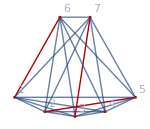

```mathematica
GraphFromSymbol[v16x25x37x4]
```

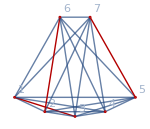

```mathematica
GraphFromSymbol[v13x26x4x57]
```

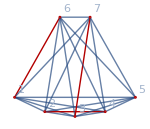
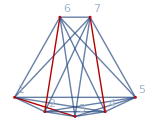
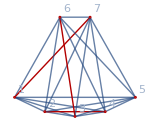
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodesTwo[7],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],2]]
```

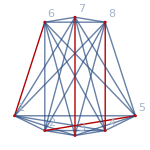

```mathematica
GraphFromSymbol[v16x25x37x48]
```

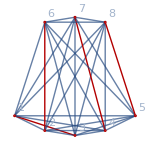

```mathematica
GraphFromSymbol[v13x26x47x58]
```

## Those who do not generate a triangle

```mathematica
Select[ShowForNodesTwo[7],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&]
```

{{{v16x24x37x5,v13x26x47x5},{{{1,3},{2,6},{4,7},{5}},{{1,6},{2,4},{3,7},{5}}}},{{v17x24x36x5,v13x26x47x5},{{{1,3},{2,6},{4,7},{5}},{{1,7},{2,4},{3,6},{5}}}},{{v16x24x37x5,v13x27x46x5},{{{1,3},{2,7},{4,6},{5}},{{1,6},{2,4},{3,7},{5}}}},{{v17x24x36x5,v13x27x46x5},{{{1,3},{2,7},{4,6},{5}},{{1,7},{2,4},{3,6},{5}}}}}

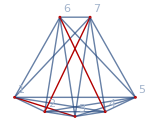
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodesTwo[7],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],4]]
```

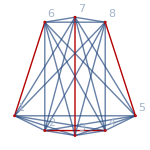
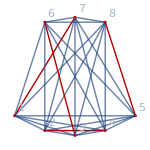
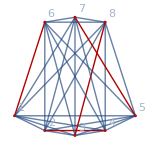
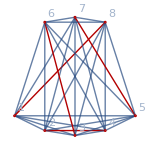
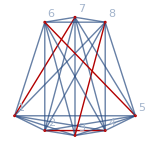
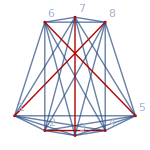
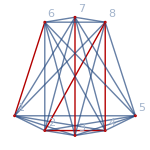
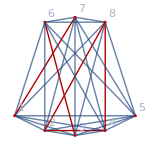
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodesTwo[8],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],20]]
```

```mathematica
Clear[ShowForNodes3];ShowForNodes3[nodes_]:=Flatten[Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]]
},
{Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3]]]], SymbolLevel[#]==4&],{part1,part2,part3}}
]
,

{part1,Take[QuadrilateralsWithPattern[nodes,1],2]},
{part2,Take[QuadrilateralsWithPattern[nodes,2],2]},
{part3,Take[QuadrilateralsWithPattern[nodes,5],2]}
],2]
```

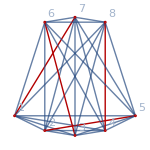
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Map[Map[GraphFromSymbol[#]&,#[[1]]]&,Take[Select[ShowForNodes3[8],Length[Select[#[[1]],HasTrianglePattern[SymbolToSets[#]]&]]==0&],4]]
```